```mathematica
Guy Mongelli							ChE 413 TA
Prof. Anthamatten						1/31/2010

Assignment #1 Solutions
```

```mathematica
Problem #1
```

```mathematica
Clear[VLJ,F,ϵ,σ]
```

```mathematica
VLJ[r_]:=4ϵ((σ/r)^12-(σ/r)^6)
```

```mathematica
F[r_]=-D[VLJ[r],r]
```

-4 ϵ ((6 σ^6)/r^7-(12 σ^12)/r^13)

```mathematica
Clear[ϵ,σ]
Solve[F[r]==0,r,Assumptions[r>0,Element[r,Reals]]]
```

{{r→-2^(1/6) σ},{r→2^(1/6) σ},{r→-(-1)^(1/3) 2^(1/6) σ},{r→(-1)^(1/3) 2^(1/6) σ},{r→-(-1)^(2/3) 2^(1/6) σ},{r→(-1)^(2/3) 2^(1/6) σ}}

```mathematica
Consider argon gas : (See Table E.1 of 'Transport Phenomena' by BSL for constants)
```

```mathematica
ϵ=3.432 (*Angstroms*)
σ(*/K*)=122.4
```

3.432

122.4

```mathematica
FullSimplify[F[r]]
```

(1.8628×10^27-2.76979×10^14 r^6)/r^13

```mathematica
Solve[F[r]==0,r,Assumptions[r>0,Element[r,Reals]]]
```

{{r→-137.389},{r→-68.6947-118.983 ⅈ},{r→-68.6947+118.983 ⅈ},{r→68.6947-118.983 ⅈ},{r→68.6947+118.983 ⅈ},{r→137.389}}

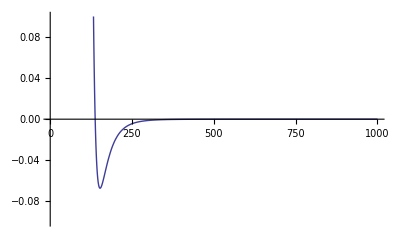

```mathematica
Plot[F[r],{r,1,1000},PlotRange->.1]
```

```mathematica
The above force is actually the force multiplied by Boltzman's constant since that was 
not accounted for in the zero-potential point, σ. Nonetheless, the observed trend stands.
```

```mathematica
Problem #2
```

```mathematica
Part A) From classical thermodynamics we know that the entropy change for an ideal gas undergoing 
an isothermal process is:
ΔS=n R Ln(Subscript[V, f]/Subscript[V, i]).
Starting with the following definition of entropy
```

```mathematica
For an isothermal process, dU is zero and we substitute for P/T using the ideal gas law (P/T=nR/V).  integrating yeilds the above result.
Part B) The definition of an adiabatic process is one that operates with a constant entropy.Therefore the entropy change is zero.
```

```mathematica
Problem #3
```

```mathematica
U/V= -(1/2) N^2∫_d^∞ V(R)ⅆτ
```

```mathematica
let V(R)=C6/R^6 and N=(NA*ρ)/M
Evaluation of the integrad at the infintessimal limit goes to zero, leaving only the other term.
U/V= (-2/3) (NA^2/(d^3 M^2))ρ^2C6
```

```mathematica
Guy Mongelli							ChE 413 TA
Prof. Anthamatten						1/31/2010

Assignment #1 Solutions
```

```mathematica
Problem #1
```

```mathematica
Clear[VLJ,F,ϵ,σ]
```

```mathematica
VLJ[r_]:=4ϵ((σ/r)^12-(σ/r)^6)
```

```mathematica
F[r_]=-D[VLJ[r],r]
```

-4 ϵ ((6 σ^6)/r^7-(12 σ^12)/r^13)

```mathematica
Clear[ϵ,σ]
Solve[F[r]==0,r,Assumptions[r>0,Element[r,Reals]]]
```

{{r→-2^(1/6) σ},{r→2^(1/6) σ},{r→-(-1)^(1/3) 2^(1/6) σ},{r→(-1)^(1/3) 2^(1/6) σ},{r→-(-1)^(2/3) 2^(1/6) σ},{r→(-1)^(2/3) 2^(1/6) σ}}

```mathematica
Consider argon gas : (See Table E.1 of 'Transport Phenomena' by BSL for constants)
```

```mathematica
ϵ=3.432 (*Angstroms*)
σ(*/K*)=122.4
```

3.432

122.4

```mathematica
FullSimplify[F[r]]
```

(1.8628×10^27-2.76979×10^14 r^6)/r^13

```mathematica
Solve[F[r]==0,r,Assumptions[r>0,Element[r,Reals]]]
```

{{r→-137.389},{r→-68.6947-118.983 ⅈ},{r→-68.6947+118.983 ⅈ},{r→68.6947-118.983 ⅈ},{r→68.6947+118.983 ⅈ},{r→137.389}}

```mathematica
Plot[F[r],{r,1,1000},PlotRange->.1]
```

-Graphics-

```mathematica
The above force is actually the force multiplied by Boltzman's constant since that was 
not accounted for in the zero-potential point, σ. Nonetheless, the observed trend stands.
```

```mathematica
Problem #2
```

```mathematica
Part A) From classical thermodynamics we know that the entropy change for an ideal gas undergoing 
an isothermal process is:
ΔS=N Subscript[k, B] Ln(Subscript[V, f]/Subscript[V, i]), where:
N=Avogadro's Number
Subscript[k, B]=Boltzman constant
Subscript[V, f]=final volume
Subscript[V, i]=initial volume
Note: N*Subscript[k, B]=R

We derive this relationship starting from the following definition of entropy change:
```

```mathematica
For an isothermal process, dU is zero.  For the second term, we substitute for P/T using the ideal gas law (P/T=nR/V).  Integrating yeilds the above result.

Part B) The definition of an adiabatic process is one that operates with a constant entropy (a.k.a. isentropic). Therefore the entropy change is zero.
```

```mathematica
Problem #3
```

```mathematica
The C.E.D. as a way to quantify the intermolecular energy within a specified volume element.  It is the difference between the average energy of the atoms in the solid crystal versus in a free state (an ideal gas at the same temperature).  The exact cohesive energy density is computed via summation of the interatomic potentials of one atom with every other atom in the lattice.  The interation of the jth atom with all of the other N-1 atoms can be written:
Subscript[U, j]=∑_(i=1,i≠j)^N V(Subscript[d, i]), where Subscript[d, i] is the distance to the ith atom.  Summing this for every atom in the lattice will double count the energies present.  Therefore the total energy is written:
U=1/2∑_(j=1)^N Subscript[U, j]
Since there are N partices in the lattice:
U=1/2NSubscript[U, j]
Since the particles are uniformly distributed in the 3D solid, this potential can be represened by a constant particle density function n multiplied by the potential per space coordinate for a particular particle.
Subscript[U, j]=∫_V N V(R)ⅆr.
Since we lose energy when we remove the atom from the lattice, the cohesive energy is negative.  Putting this together we get:
U=-(1/2) N^2∫_V V(R)ⅆr
```

```mathematica
Let the potential generated by an interatomic interaction  be V(R)=Subscript[C, 6]/R^6 and N=(Subscript[N, A]*ρ)/M, where:
Subscript[C, 6]=an arbitrary constant
Subscript[N, A]=Avogadro's Number (molecules/mol)
ρ=density (g/L^3)
M=molecular weight (g/mol)
This implies N has units (molecules/L^3)

To perform this integration we much expand into 3D space with a triple integral in spherical coordinates.  The appropriate change of variables is dτ=4πR^2 dr
U=-(1/2) N^2∫Subscript[C, 6]/R^6 4 πR^2 ⅆr
Evaluation of the integrad at the infinte limit goes to zero, leaving only the other term.  This is the result:
U/V= (-2π/3) (Subscript[N, A]^2/(d^3 M^2))ρ^2Subscript[C, 6]
```

```mathematica
Guy Mongelli                                                                              ChE 413
Prof. Anthamatten                                                                      2/18/2011

Problem Set #2
```

```mathematica
Problem #1
```

```mathematica
ClearAll[σ,ϵ]
```

```mathematica
ω=10*2π (* Hz *);
ϵ0=.01;
σ0=80;
δ=π/6;
```

```mathematica
σ[t_]:=σ0*Sin[ω*t+δ];
ϵ[t_]:=ϵ0*Sin[ω*t];
```

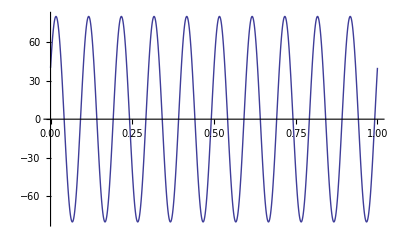

```mathematica
Plot[{σ[t]},{t,0,1}]
```

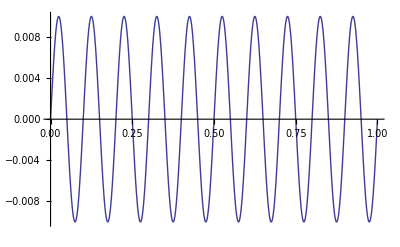

```mathematica
Plot[{ϵ[t]},{t,0,1}]
```

```mathematica
StorageMod=σ0/ϵ0*Cos[δ]
```

6928.2

```mathematica
LossMod=σ0/ϵ0*Sin[δ]
```

4000.

```mathematica
PhaseAngle=LossMod/StorageMod
```

0.57735

```mathematica
For a perfect elastic solid, the strain and stress curves are perfectly in phase.  For a purly viscous liquid, the phase angle is 90 degrees.  The materials that genereted this DMA data is clearly viscoelastic.
```

```mathematica
Problem #2
```

```mathematica
ϵ=30/(6.02*10^23) (* kJ/mol *);
a=4 (* Angstroms *);
```

```mathematica
Clear[A]
```

```mathematica
The constant defined in the Young' s modulus equation on page 14 of R.A.L. Jones is somewhat nebulous.  However, we can assume any potential form (VanDerWalls's may be specifically relevant) to determine f ''[1].  The constant of proportionality, C6, is the polarization of our soft matter spheres raised to the second power. Literature values exist for  different organic and soft matter materials.   For further interest see: "Mean polarizabilities of organic molecules. A comparison of Restricted Hartree Fock, Density Functional Theory and Direct Reaction Field
results." Journal of Molecular Structure (Theochem) 458 (1999) 11–17
```

```mathematica
CED=(6*ϵ)/a^3(* kJ/cubic angstrom *)
```

4.67193×10^-24

```mathematica
A[r_]=D[D[f[r],r],r]
```

(42 α^2)/r^8

```mathematica
YoungMod=(f''[1]*ϵ)/a^3
```

7.78654×10^-25 f''[1]

```mathematica
CED/YoungMod
```

6./f''[1]

```mathematica
It is important to note that the Young's Modulus of this theoretical solid is not numerically idential to the C.E.D, but that these two values are proportianal and follow a simmilar trend.  That trend is that the higher the interatomic forces (energy density) of the material, the larger the Young' s modulus (i.e. more stress is required to acheive the same strain ratio value).
```

```mathematica
Problem #3

-Graphics-                                   -Graphics-
              Melamine                                                                        Cyanuric Acid                    


                   -Graphics-
Hydrogen bonding between melamine and cyanuric acid

http://www.who.int/foodsafety/fs_management/infosan_events/en/index.html

Enthalpies of Hydrogen Bonding in different species:
O—H...:O (21 kJ/mol or 5.0 kcal/mol)
N—H...:N (13 kJ/mol or 3.1 kcal/mol)
N—H...:O (8 kJ/mol or 1.9 kcal/mol)

A complete answer discussed several of the following key points supported by scientific references:
(1) Melamine addition was the result of an illegal attempt by certain (over 20!) Chinese companies to increase the apparent nitrogen content of foods. The nitrogen content was introduces to falsely simulate that of natural protien in milk and egg products.
(2) The malamine/cyanuric acid "hetero" dimer crystallized much more readily than the melamine-homo dimer in a low pH enviornment due more energy stability generated by hydrogen bonding (roughly correlates to the electronegativity difference between N and O).
(3) Studies in dogs and cats by various researchers has shown that these crystallizations can lead to acute to severe impairment of kidney function (potentially fatal), kidney stone formation, and even rupture of blood cells (Wang C, et al. "Hemolysis of human erythrocytes induced by malamine-cyanurate complex."  Biochemical and Biophysical Research Communications [Nov 2010]) on the basis of severity and duration of exposure.
```

```mathematica
Problem #4
Please see the attatched excel spreadsheet.
```

```mathematica
Guy Mongelli                                                                                ChE 413 TA
Prof. Anthamatten                                                                        3/7/2011
```

```mathematica
Assignment #3
```

```mathematica
Problem #1 (R.A.L. Jones Problem 3.1)
Part A: The critical point is the temperature at which the spinodal and binodal decompositions become unique.  In other words, a spinodal transition does not exist below a certain temperature.  This occurs when the interaction perameter is greater than or equal to 2 (see p. 29-29).  Given the 'equation of state' for the system as follows
```

```mathematica
χ[T_]=600/T;
```

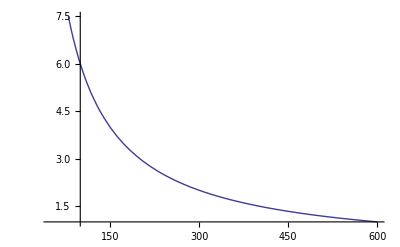

```mathematica
Plot[χ[T],{T,50,600}]
```

```mathematica
Solve[χ[T]==2,T]
```

{{T→300}}

```mathematica
Part B : We will rewrite F[Subscript[ϕ, A],Subscript[ϕ, B]]/(Subscript[k, B] T) as Φ[Subscript[ϕ, A],Subscript[ϕ, B]].
```

```mathematica
Φ[ϕA_,ϕB_,T_]=ϕA*Log[ϕA]+ϕB*Log[ϕB]+χ[T]*ϕA*ϕB;
```

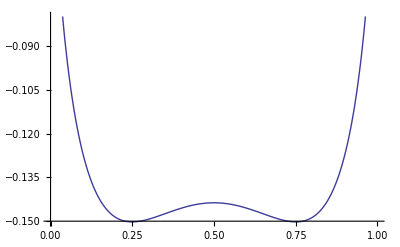

```mathematica
Plot[Φ[ϕA,1-ϕA,273],{ϕA,0,1}]
```

```mathematica
Manipulate[Plot[Φ[ϕA,1-ϕA,T],{ϕA,0,1},PlotRange->{-.5,.5}],{T,200,600}]
```

```mathematica
We will eliminate ϕB due to ϕA + ϕB = 1
```

```mathematica
Clear[T]
```

```mathematica
FullSimplify[Φ[ϕA,1-ϕA,T]]
```

-((-1+ϕA) (600 ϕA+T Log[1-ϕA]))/T+ϕA Log[ϕA]

```mathematica
Part B : To find the binodal decomposition, we compute the point of zero slope (more, generally the point of tangency).  Therefore, we find the zero point of the first derivative.  Note that it is zero at ϕA=.5, however, we do not consider this point a true solution since it is unstable.
```

```mathematica
χ[273]
```

200/91

```mathematica
N[χ[273],3]
```

2.2

```mathematica
D[Φ[.2497,1-.2497,273],ϕA]
```

0

```mathematica
D[Φ[.5,.5,273],ϕA]
```

0

```mathematica
Plot[D[Φ[ϕA,1-ϕA,273]],{ϕA,0,1}]
```

-Graphics-

```mathematica
Part C : To find the spinodal decomposition volume fractions, we search for points when the second derivative is zero.
```

```mathematica
Solve[{D[D[Φ[ϕA,ϕB,273],ϕA],ϕA]==0},ϕA]
```

{{ϕA→7/20},{ϕA→13/20}}

```mathematica
N[7/20,3]
```

0.35

```mathematica
N[13/20,3]
```

0.65

```mathematica
Problem #2 (R.A.L. Jones 3.2): This problem requires looking at solutions to the binodal decomposition for a more general case.  Since the chi value is large and positive, we know the volume fraction (ϕA) will be small.
```

```mathematica
Clear[χ]
```

```mathematica
Simplify[D[ϕA*Log[ϕA]+(1-ϕA)*Log[1-ϕA]+χ[T]*ϕA*(1-ϕA),ϕA]]
```

-Log[1-ϕA]+Log[ϕA]+χ[T]-2 ϕA χ[T]

```mathematica
Since ϕA is small, we can assume it is zero.  Therefore, (1-ϕA)≈1 and Log[1-ϕA]≈0.  Also, (1-2*ϕA)≈1.  This gives Log(ϕA)+χ=0.  This is easily rearranged to ϕA=Exp[-χ].
```

```mathematica
Problem #3 (R.A.L Jones 3.3):
```

```mathematica
χ1[nc_]=3.04+1.37*nc
```

3.04+1.37 nc

```mathematica
χ1[1]
```

4.41

```mathematica
Φ1[ϕA_,ϕB_,nc_]=ϕA*Log[ϕA]+ϕB*Log[ϕB]+χ[T]*ϕ1[nc]*ϕB;
```

```mathematica
coeffs=Table[{i,χ1[i],Exp[-χ1[i]]},{i,1,10}];
TableForm[coeffs,,TableHeadings->{None,{"nc","χ1[nc]","Exp[-χ1[i]]"}}]
```

nc | χ1[nc] | Exp[-χ1[i]]
1 | 4.41 | 0.0121552
2 | 5.78 | 0.00308872
3 | 7.15 | 0.000784864
4 | 8.52 | 0.000199439
5 | 9.89 | 0.0000506789
6 | 11.26 | 0.0000128779
7 | 12.63 | 3.27236×10^-6
8 | 14. | 8.31529×10^-7
9 | 15.37 | 2.11297×10^-7
10 | 16.74 | 5.36921×10^-8

```mathematica
The observed trend is that longer alkane chains will be increasingly insoluble in water.
```

```mathematica
Problem #4 (R.A.L. Jones 3.4): For this problem we consider a sharp transition since these compounds have strong tendencies toward phase separation.  The governing equation is discussed on p. 32
```

```mathematica
χ=14;
kB=1.3806503×10^-23(*J/K*);
T=273 (*K*);
υ=2.36*10^-29 (*m3*);
```

```mathematica
Clear[γ]
```

```mathematica
γ[z_]=(χ*kB*T)/(z*υ^(2/3))
```

0.641357/z

```mathematica
The only variable left to input is z, the coordination number.  Since the intermolecular forces will  be between the hydrogen atoms on the octane and the oxygen atoms in water, we will consider how many  oygen atoms can coordinate with an octane molecule.  There are 18 hydrogens present, so it will be approxamately 18.  THere may be slightly more or less.  The surface tension does not change much over the domain of z from [16, 20].
```

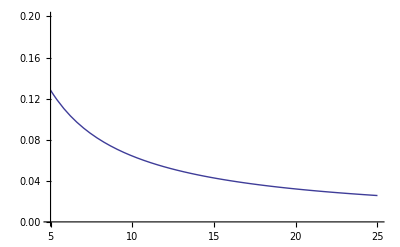

```mathematica
Plot[γ[z],{z,5,25},PlotRange->{0,.2}]
```

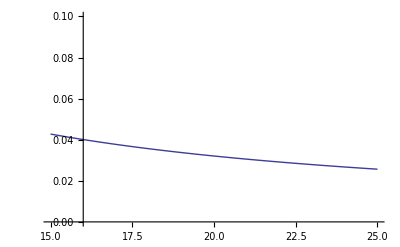

```mathematica
Plot[γ[z],{z,15,25},PlotRange->{0,.1}]
```

```mathematica
The units for the sharp surface tension are J/m^3
```

```mathematica
γ[18]
```

0.0356309

```mathematica
γ[20]
```

0.0320678

```mathematica
Guy Mongelli                                                                    ChE 413 TA
Prof. Anthamatten                                                        3/8/2011
```

413 ChE Guy Mongelli TA

(3 Prof.Anthamatten)/16088

```mathematica
Assignment #4
```

Assignment #4

```mathematica
The following particulate properties are given.  Quantities denoted with a 1 are for the sand grain, denoted 2 are for the polymer particle, denoted 3 are for the virus particle.
```

```mathematica
ρ0=1.002*10^-3 (* kg/m3 *);
```

```mathematica
ρ1=2200 (* kg/m3 *);
a1=1*10^-4/2 (* m *);
ρ2=1050 (* kg/m3 *);
a2=10^-6 /2(* m *);
ρ3=1020 (* kg/m3 *);
a3=50 *10^-9/2 (* m *);
```

```mathematica
The following line computes the numerical values of the particle radii :
```

```mathematica
Evaluate[N[a1,3],N[a2,3],N[a3,3]]
```

Sequence[0.00005,5.×10^-7,2.5×10^-8]

```mathematica
The governing equation is (p. 50) :
```

```mathematica
kB=1.380×10^-23 (* J/K *);
g=9.80665 (* m2/s *);
η=1.002*10^-3 (* Pa*s *);
ρ0=1000 (* kg/m3 *);
```

```mathematica
The units for terminal velocity are m/s.
```

```mathematica
vt1=(2*a1^2(ρ1-ρ0)*g)/(9*η)
```

0.00652472

```mathematica
vt2=(2*a2^2(ρ2-ρ0)*g)/(9*η)
```

2.71863×10^-8

```mathematica
vt3=(2*a3^2(ρ3-ρ0)*g)/(9*η)
```

2.71863×10^-11

```mathematica
This terminal velocity is correct. The one in the back of the book is not.
```

```mathematica
The units for the Stokes - Einstein diffusion coefficient are m^2/s.
```

```mathematica
DSE1[T_]=(kB*T)/(6π*a1*η)
```

1.4613×10^-17 T

```mathematica
DSE1[273]
```

3.98936×10^-15

```mathematica
DSE2[T_]=(kB*T)/(6π*a2*η)
```

1.4613×10^-15 T

```mathematica
DSE2[273]
```

3.98936×10^-13

```mathematica
DSE3[T_]=(kB*T)/(6π*a3*η)
```

2.92261×10^-14 T

```mathematica
DSE3[273]
```

7.97871×10^-12

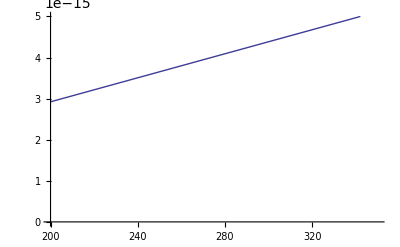

```mathematica
Plot[DSE1[T],{T,200,350},PlotRange->{0,5*10^-15}]
```

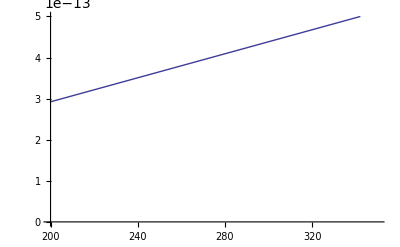

```mathematica
Plot[DSE2[T],{T,200,350},PlotRange->{0,5*10^-13}]
```

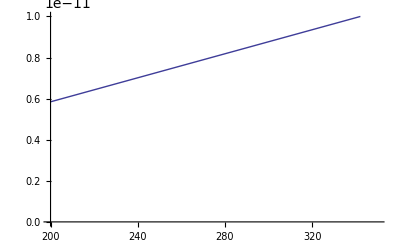

```mathematica
Plot[DSE3[T],{T,200,350},PlotRange->{0,1*10^-11}]
```

```mathematica
The units for the diffusion times are in seconds.
```

```mathematica
τD1[T_]=a1^2/DSE1[T]
```

(1.7108×10^8)/T

```mathematica
τD1[273]
```

626667.

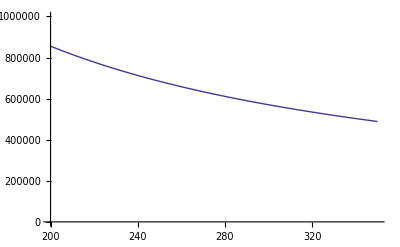

```mathematica
Plot[τD1[T],{T,200,350},PlotRange->{0,10^6}]
```

```mathematica
τD2[T_]=a2^2/DSE2[T]
```

171.08/T

```mathematica
τD2[273]
```

0.626667

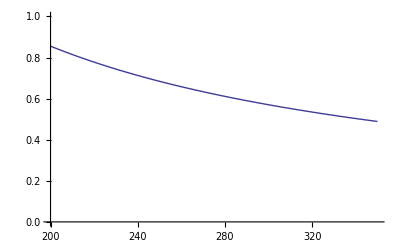

```mathematica
Plot[τD2[T],{T,200,350},PlotRange->{0,1}]
```

```mathematica
τD3[T_]=a3^2/DSE3[T]
```

0.021385/T

```mathematica
τD3[273]
```

0.0000783334

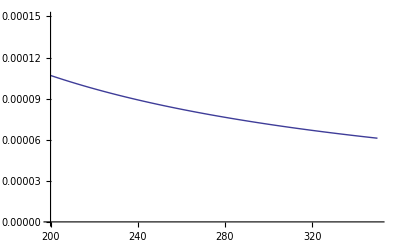

```mathematica
Plot[τD3[T],{T,200,350},PlotRange->{0,1.5*10^-4}]
```

```mathematica
Problem #3 (R.A.L. Jones 4.4)
```

4.4 Problem R.A.L.Jones #3

```mathematica
Part A: The Debye screening legnth is one over kappa, where kappa for salt in water (p. 59) (one cubic decimeter is one liter):
```

```mathematica
Iconc[1]=10^-5 (*mol/L *);
Iconc[2]=10^-4 (*mol/L *);
Iconc[3]=10^-3 (*mol/L *);
Iconc[4]=10^-2 (*mol/L *);
Iconc[5]=10^-1 (*mol/L *);
```

```mathematica
κ[i_]=.304(Iconc[i])^(-1/2)
```

0.304/(√Iconc[i])

```mathematica
The Debye screening legnth is is nanometers.
```

```mathematica
Evaluate[N[κ[1],3],N[κ[2],3],N[κ[3],3],N[κ[4],3],N[κ[5],3]]
```

Sequence[96.1332,30.4,9.61332,3.04,0.961332]

```mathematica
Evaluate[N[1/κ[1],3],N  [1/κ[2],3],N[1/κ[3],3],N[1/κ[4],3],N[1/κ[5],3]]
```

Sequence[0.0104022,0.0328947,0.104022,0.328947,1.04022]

```mathematica
Evaluate[N[10^-9/κ[1],3],N[10^-9/κ[2],3],N[10^-9/κ[3],3],N[10^-9/κ[4],3],N[10^-9/κ[5],3]]
```

Sequence[1.04022×10^-11,3.28947×10^-11,1.04022×10^-10,3.28947×10^-10,1.04022×10^-9]

```mathematica
The trend is that decreasing the salt concentration will increase the distance until charge is screened.
```

```mathematica
Part B :  Utilize Figure 4.8 (assuming that the surface charge and volume are simmilar to NaCl)
```

Part (B:4.8 and are assuming charge Figure NaCl simmilar surface that the to Utilize volume)

```mathematica
VolFrac[1]=.03 ;
VolFrac[2]=.1 ;
VolFrac[3]=.3 ;
VolFrac[4]=.5 ;
VolFrac[5]=.55 ;
```

```mathematica
Guy Mongelli                                             ChE 413 TA
Prof. Anthamatten                                        3/8/2011
```

413 ChE Guy Mongelli TA

(3 Prof.Anthamatten)/16088

```mathematica
Assignment #4
```

Assignment #4

```mathematica
The following particulate properties are given.  Quantities denoted with a 1 are for the sand grain, denoted 2 are for the polymer particle, denoted 3 are for the virus particle.
```

```mathematica
ρ0=1.002*10^-3 (* kg/m3 *);
```

```mathematica
ρ1=2200 (* kg/m3 *);
a1=1*10^-4/2 (* m *);
ρ2=1050 (* kg/m3 *);
a2=10^-6 /2(* m *);
ρ3=1020 (* kg/m3 *);
a3=50 *10^-9/2 (* m *);
```

```mathematica
The following line computes the numerical values of the particle radii :
```

```mathematica
Evaluate[N[a1,3],N[a2,3],N[a3,3]]
```

Sequence[0.00005,5.×10^-7,2.5×10^-8]

```mathematica
The governing equation is (p. 50) :
```

```mathematica
kB=1.380×10^-23 (* J/K *);
g=9.80665 (* m2/s *);
η=1.002*10^-3 (* Pa*s *);
ρ0=1000 (* kg/m3 *);
```

```mathematica
The units for terminal velocity are m/s.
```

```mathematica
vt1=(2*a1^2(ρ1-ρ0)*g)/(9*η)
```

0.00652472

```mathematica
vt2=(2*a2^2(ρ2-ρ0)*g)/(9*η)
```

2.71863×10^-8

```mathematica
vt3=(2*a3^2(ρ3-ρ0)*g)/(9*η)
```

2.71863×10^-11

```mathematica
This terminal velocity is correct. The one in the back of the book is not.
```

```mathematica
The units for the Stokes - Einstein diffusion coefficient are m^2/s.
```

```mathematica
DSE1[T_]=(kB*T)/(6π*a1*η)
```

1.4613×10^-17 T

```mathematica
DSE1[273]/60/60/24/365
```

1.26502×10^-22

```mathematica
DSE2[T_]=(kB*T)/(6π*a2*η)
```

1.4613×10^-15 T

```mathematica
DSE2[273]
```

3.98936×10^-13

```mathematica
DSE3[T_]=(kB*T)/(6π*a3*η)
```

2.92261×10^-14 T

```mathematica
DSE3[273]
```

7.97871×10^-12

```mathematica
Plot[DSE1[T],{T,200,350},PlotRange->{0,5*10^-15}]
```

-Graphics-

```mathematica
Plot[DSE2[T],{T,200,350},PlotRange->{0,5*10^-13}]
```

-Graphics-

```mathematica
Plot[DSE3[T],{T,200,350},PlotRange->{0,1*10^-11}]
```

-Graphics-

```mathematica
The units for the diffusion times are in seconds.
```

```mathematica
τD1[T_]=a1^2/DSE1[T]
```

(1.7108×10^8)/T

```mathematica
τD1[273]
```

626667.

```mathematica
Plot[τD1[T],{T,200,350},PlotRange->{0,10^6}]
```

-Graphics-

```mathematica
τD2[T_]=a2^2/DSE2[T]
```

171.08/T

```mathematica
τD2[273]
```

0.626667

```mathematica
Plot[τD2[T],{T,200,350},PlotRange->{0,1}]
```

-Graphics-

```mathematica
τD3[T_]=a3^2/DSE3[T]
```

0.021385/T

```mathematica
τD3[273]
```

0.0000783334

```mathematica
Plot[τD3[T],{T,200,350},PlotRange->{0,1.5*10^-4}]
```

-Graphics-

```mathematica
Problem #3 (R.A.L. Jones 4.4)
```

4.4 Problem R.A.L.Jones #3

```mathematica
Part A: The Debye screening legnth is one over kappa, where kappa for salt in water (p. 59) (one cubic decimeter is one liter):
```

```mathematica
Iconc[1]=10^-5 (*mol/L *);
Iconc[2]=10^-4 (*mol/L *);
Iconc[3]=10^-3 (*mol/L *);
Iconc[4]=10^-2 (*mol/L *);
Iconc[5]=10^-1 (*mol/L *);
```

```mathematica
κ[i_]=1/(.304(Iconc[i])^(-1/2))
```

3.28947 √Iconc[i]

```mathematica
κ2[i_]=1/(.304(i)^(-1/2))
```

3.28947 √i

```mathematica
1/κ2[10^-5]
```

96.1332

```mathematica
The Debye screening legnth is is nanometers.
```

```mathematica
Evaluate[N[1/κ[1],3],N[1/κ[2],3],N[1/κ[3],3],N[1/κ[4],3],N[1/κ[5],3]]
```

Sequence[96.1332,30.4,9.61332,3.04,0.961332]

```mathematica
The trend is that decreasing the salt concentration will increase the distance until charge is screened.
```

```mathematica
Part B :  Utilize Figure 4.8 (assuming that the surface charge and volume are simmilar to NaCl)
```

Part (B:4.8 and are assuming charge Figure NaCl simmilar surface that the to Utilize volume)

```mathematica
VolFrac[1]=.03 ;
VolFrac[2]=.1 ;
VolFrac[3]=.3 ;
VolFrac[4]=.5 ;
VolFrac[5]=.55 ;
```

```mathematica
Guy Mongelli                                             ChE 413 TA
Prof. Anthamatten                                        3/8/2011
```

413 ChE Guy Mongelli TA

(3 Prof.Anthamatten)/16088

```mathematica
Assignment #4
```

Assignment #4

```mathematica
The following particulate properties are given.  Quantities denoted with a 1 are for the sand grain, denoted 2 are for the polymer particle, denoted 3 are for the virus particle.
```

```mathematica
ρ0=1.002*10^-3 (* kg/m3 *);
```

```mathematica
ρ1=2200 (* kg/m3 *);
a1=1*10^-4/2 (* m *);
ρ2=1050 (* kg/m3 *);
a2=10^-6 /2(* m *);
ρ3=1020 (* kg/m3 *);
a3=50 *10^-9/2 (* m *);
```

```mathematica
The following line computes the numerical values of the particle radii :
```

```mathematica
Evaluate[N[a1,3],N[a2,3],N[a3,3]]
```

Sequence[0.00005,5.×10^-7,2.5×10^-8]

```mathematica
The governing equation is (p. 50) :
```

```mathematica
kB=1.380×10^-23 (* J/K *);
g=9.80665 (* m2/s *);
η=1.002*10^-3 (* Pa*s *);
ρ0=1000 (* kg/m3 *);
```

```mathematica
The units for terminal velocity are m/s.
```

```mathematica
vt1=(2*a1^2(ρ1-ρ0)*g)/(9*η)
```

0.00652472

```mathematica
vt2=(2*a2^2(ρ2-ρ0)*g)/(9*η)
```

2.71863×10^-8

```mathematica
vt3=(2*a3^2(ρ3-ρ0)*g)/(9*η)
```

2.71863×10^-11

```mathematica
This terminal velocity is correct. The one in the back of the book is not.
```

```mathematica
The units for the Stokes - Einstein diffusion coefficient are m^2/s.
```

```mathematica
DSE1[T_]=(kB*T)/(6π*a1*η)
```

1.4613×10^-17 T

```mathematica
DSE1[273]/60/60/24/365
```

1.26502×10^-22

```mathematica
DSE2[T_]=(kB*T)/(6π*a2*η)
```

1.4613×10^-15 T

```mathematica
DSE2[273]
```

3.98936×10^-13

```mathematica
DSE3[T_]=(kB*T)/(6π*a3*η)
```

2.92261×10^-14 T

```mathematica
DSE3[273]
```

7.97871×10^-12

```mathematica
Plot[DSE1[T],{T,200,350},PlotRange->{0,5*10^-15}]
```

-Graphics-

```mathematica
Plot[DSE2[T],{T,200,350},PlotRange->{0,5*10^-13}]
```

-Graphics-

```mathematica
Plot[DSE3[T],{T,200,350},PlotRange->{0,1*10^-11}]
```

-Graphics-

```mathematica
The units for the diffusion times are in seconds.
```

```mathematica
τD1[T_]=a1^2/DSE1[T]
```

(1.7108×10^8)/T

```mathematica
τD1[273]
```

626667.

```mathematica
Plot[τD1[T],{T,200,350},PlotRange->{0,10^6}]
```

-Graphics-

```mathematica
τD2[T_]=a2^2/DSE2[T]
```

171.08/T

```mathematica
τD2[273]
```

0.626667

```mathematica
Plot[τD2[T],{T,200,350},PlotRange->{0,1}]
```

-Graphics-

```mathematica
τD3[T_]=a3^2/DSE3[T]
```

0.021385/T

```mathematica
τD3[273]
```

0.0000783334

```mathematica
Plot[τD3[T],{T,200,350},PlotRange->{0,1.5*10^-4}]
```

-Graphics-

```mathematica
Problem #3 (R.A.L. Jones 4.4)
```

4.4 Problem R.A.L.Jones #3

```mathematica
Part A: The Debye screening legnth is one over kappa, where kappa for salt in water (p. 59) (one cubic decimeter is one liter):
```

```mathematica
Iconc[1]=10^-5 (*mol/L *);
Iconc[2]=10^-4 (*mol/L *);
Iconc[3]=10^-3 (*mol/L *);
Iconc[4]=10^-2 (*mol/L *);
Iconc[5]=10^-1 (*mol/L *);
```

```mathematica
κ[i_]=1/(.304(Iconc[i])^(-1/2))
```

3.28947 √Iconc[i]

```mathematica
κ2[i_]=1/(.304(i)^(-1/2))
```

3.28947 √i

```mathematica
1/κ2[10^-5]
```

96.1332

```mathematica
The Debye screening legnth is is nanometers.
```

```mathematica
Evaluate[N[1/κ[1],3],N[1/κ[2],3],N[1/κ[3],3],N[1/κ[4],3],N[1/κ[5],3]]
```

Sequence[96.1332,30.4,9.61332,3.04,0.961332]

```mathematica
The trend is that decreasing the salt concentration will increase the distance until charge is screened.
```

```mathematica
Part B :  Utilize Figure 4.8 (assuming that the surface charge and volume are simmilar to NaCl)
```

Part (B:4.8 and are assuming charge Figure NaCl simmilar surface that the to Utilize volume)

```mathematica
VolFrac[1]=.03 ;
VolFrac[2]=.1 ;
VolFrac[3]=.3 ;
VolFrac[4]=.5 ;
VolFrac[5]=.55 ;
```

```mathematica
Guy Mongelli                                                                    ChE 413 TA
Prof. Anthamatten                                                        3/8/2011
```

413 ChE Guy Mongelli TA

(3 Prof.Anthamatten)/16088

```mathematica
Assignment #4
```

Assignment #4

```mathematica
The following particulate properties are given.  Quantities denoted with a 1 are for the sand grain, denoted 2 are for the polymer particle, denoted 3 are for the virus particle.
```

```mathematica
ρ0=1.002*10^-3 (* kg/m3 *);
```

```mathematica
ρ1=2200 (* kg/m3 *);
a1=1*10^-4/2 (* m *);
ρ2=1050 (* kg/m3 *);
a2=10^-6 /2(* m *);
ρ3=1020 (* kg/m3 *);
a3=50 *10^-9/2 (* m *);
```

```mathematica
The following line computes the numerical values of the particle radii :
```

```mathematica
Evaluate[N[a1,3],N[a2,3],N[a3,3]]
```

Sequence[0.00005,5.×10^-7,2.5×10^-8]

```mathematica
The governing equation is (p. 50) :
```

```mathematica
kB=1.380×10^-23 (* J/K *);
g=9.80665 (* m2/s *);
η=1.002*10^-3 (* Pa*s *);
ρ0=1000 (* kg/m3 *);
```

```mathematica
The units for terminal velocity are m/s.
```

```mathematica
vt1=(2*a1^2(ρ1-ρ0)*g)/(9*η)
```

0.00652472

```mathematica
vt2=(2*a2^2(ρ2-ρ0)*g)/(9*η)
```

2.71863×10^-8

```mathematica
vt3=(2*a3^2(ρ3-ρ0)*g)/(9*η)
```

2.71863×10^-11

```mathematica
This terminal velocity is correct. The one in the back of the book is not.
```

```mathematica
The units for the Stokes - Einstein diffusion coefficient are m^2/s.
```

```mathematica
DSE1[T_]=(kB*T)/(6π*a1*η)
```

1.4613×10^-17 T

```mathematica
DSE1[273]
```

3.98936×10^-15

```mathematica
DSE2[T_]=(kB*T)/(6π*a2*η)
```

1.4613×10^-15 T

```mathematica
DSE2[273]
```

3.98936×10^-13

```mathematica
DSE3[T_]=(kB*T)/(6π*a3*η)
```

2.92261×10^-14 T

```mathematica
DSE3[273]
```

7.97871×10^-12

```mathematica
Plot[DSE1[T],{T,200,350},PlotRange->{0,5*10^-15}]
```

-Graphics-

```mathematica
Plot[DSE2[T],{T,200,350},PlotRange->{0,5*10^-13}]
```

-Graphics-

```mathematica
Plot[DSE3[T],{T,200,350},PlotRange->{0,1*10^-11}]
```

-Graphics-

```mathematica
The units for the diffusion times are in seconds.
```

```mathematica
τD1[T_]=a1^2/DSE1[T]
```

(1.7108×10^8)/T

```mathematica
τD1[273]
```

626667.

```mathematica
Plot[τD1[T],{T,200,350},PlotRange->{0,10^6}]
```

-Graphics-

```mathematica
τD2[T_]=a2^2/DSE2[T]
```

171.08/T

```mathematica
τD2[273]
```

0.626667

```mathematica
Plot[τD2[T],{T,200,350},PlotRange->{0,1}]
```

-Graphics-

```mathematica
τD3[T_]=a3^2/DSE3[T]
```

0.021385/T

```mathematica
τD3[273]
```

0.0000783334

```mathematica
Plot[τD3[T],{T,200,350},PlotRange->{0,1.5*10^-4}]
```

-Graphics-

```mathematica
Problem #3 (R.A.L. Jones 4.4)
```

4.4 Problem R.A.L.Jones #3

```mathematica
Part A: The Debye screening legnth is one over kappa, where kappa for salt in water (p. 59) (one cubic decimeter is one liter):
```

```mathematica
Iconc[1]=10^-5 (*mol/L *);
Iconc[2]=10^-4 (*mol/L *);
Iconc[3]=10^-3 (*mol/L *);
Iconc[4]=10^-2 (*mol/L *);
Iconc[5]=10^-1 (*mol/L *);
```

```mathematica
κ[i_]=.304(Iconc[i])^(-1/2)
```

0.304/(√Iconc[i])

```mathematica
The Debye screening legnth is is nanometers.
```

```mathematica
Evaluate[N[κ[1],3],N[κ[2],3],N[κ[3],3],N[κ[4],3],N[κ[5],3]]
```

Sequence[96.1332,30.4,9.61332,3.04,0.961332]

```mathematica
Evaluate[N[1/κ[1],3],N  [1/κ[2],3],N[1/κ[3],3],N[1/κ[4],3],N[1/κ[5],3]]
```

Sequence[0.0104022,0.0328947,0.104022,0.328947,1.04022]

```mathematica
Evaluate[N[10^-9/κ[1],3],N[10^-9/κ[2],3],N[10^-9/κ[3],3],N[10^-9/κ[4],3],N[10^-9/κ[5],3]]
```

Sequence[1.04022×10^-11,3.28947×10^-11,1.04022×10^-10,3.28947×10^-10,1.04022×10^-9]

```mathematica
The trend is that decreasing the salt concentration will increase the distance until charge is screened.
```

```mathematica
Part B :  Utilize Figure 4.8 (assuming that the surface charge and volume are simmilar to NaCl)
```

Part (B:4.8 and are assuming charge Figure NaCl simmilar surface that the to Utilize volume)

```mathematica
VolFrac[1]=.03 ;
VolFrac[2]=.1 ;
VolFrac[3]=.3 ;
VolFrac[4]=.5 ;
VolFrac[5]=.55 ;
```

```mathematica
Guy F. Mongelli                                                                       ChE 413 TA
Prof. Anthamatten                                                                   4/17/2011
```

```mathematica
Assignment #5
```

```mathematica
Problem #1
```

```mathematica
n=10000;
a=.67 (* nm *);
```

```mathematica
Part A :  For a melt, use equation 5.5 on page 78 (r in nanometers):
```

```mathematica
r=(a^2*n)^(1/2)
```

67.

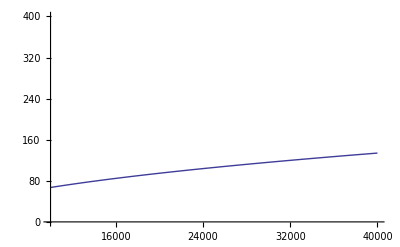

```mathematica
Plot[(a^2*N)^(1/2),{N,10000,40000},PlotRange->{0,400}]
```

```mathematica
These plots tell us that the rms end to end distance of the polymer chain is not heavily dependent on the degree of polymerization in dilute and non - interacting systems.  Since there is no energy gain (stability of the system) from the interaction of the polymer with the solvent, there is no reason for the polymer to swell, as it does in the case of a melt.
```

```mathematica
In the following lines of code, we can observe that in the non-interacting case, the rms end to end distance is more strongly dependent upon the monomer size than the degree of polymerization.  This comes into play, for example, if we are attempting to synthesize a certain size of polymer, it is often difficult to acheive a high degree of polymerization (a problem that polymer scientists face all the time and have overcome in many instances).  It may be better to select a larger monomer with simmilar functionality to increase overall particle size.  The monomer size, a, can usually be approximated from a gemetric analysis using accepted bond legnths and angles.
```

```mathematica
Manipulate[Plot[(A^2*N)^(1/2),{N,10000,40000},PlotRange->{0,600}],{A,.1,1}]
```

```mathematica
Part B : For chi equal to zero, use the cases described on page 81.  The interaction perameter for a melt is less than a half, so use case 1 (r in nanometers):
```

```mathematica
r=a*n^(3/5)
```

168.296

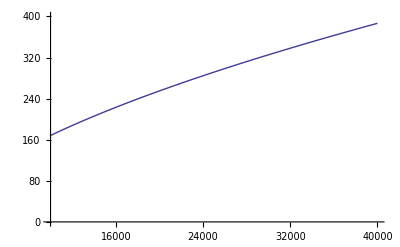

```mathematica
Plot[a*N^(3/5),{N,10000,40000},PlotRange->{0,400}]
```

```mathematica
The following lines of mathermatica code allow us to easily oberve how the stregnth of swelling behavior is dependent upon the statistical step legnth (monomer size), a.
```

```mathematica
Manipulate[Plot[A*N^(3/5),{N,10000,40000},PlotRange->{0,600}],{A,.1,1}]
```

```mathematica
Problem #3
```

```mathematica
DSolve[D[f[t],t]==k(1-f[t])^2,f,t]
```

{{f→Function[{t},(-1+k t+C[1])/(k t+C[1])]}}

```mathematica
k=4*10^-4 (* 1/s *);
```

```mathematica
f[t_]=(-1+k t)/(k t)
```

(2500 (-1+t/2500))/t

```mathematica
Simplify[f[t]]
```

(-2500+t)/t

```mathematica
z=3;
```

```mathematica
fc=1/(z-1)
```

1/2

```mathematica
FullSimplify[k(1-f[t])^2]
```

2500/t^2

```mathematica
FullSimplify[D[f[t],t]]
```

2500/t^2

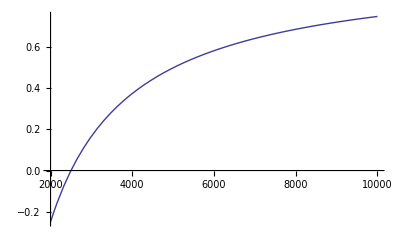

```mathematica
Plot[f[t],{t,2000,10000}]
```

```mathematica
Solve[f[t]==0,t]
```

{{t→2500}}

```mathematica
The point at which the gel fraction goes above zero is the gelation point.  This occurs at 2500 seconds.
```

```mathematica
Alternatively, we can solve this problem by integrating until the percolation theshold (p. 98) :
```

```mathematica
Solve[1/k∫_0^fc 1/(1-f)^2 ⅆf==∫_0^t0 1ⅆt,t0]
```

{{t0→2500}}

```mathematica
GelFrac[t_]=FullSimplify[1-((1-f[t])/f[t])^3]
```

1-15625000000/(-2500+t)^3

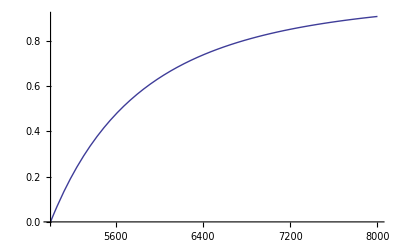

```mathematica
Plot[GelFrac[t],{t,5000,8000}]
```

```mathematica
Solve[1/(1-.75)-1==k*t,t]
```

{{t→7500.}}

```mathematica
FullSimplify[Solve[(-3/4+1)^(1/3)==1/f-1,f]]
```

{{f→1/(1+1/2^(2/3))}}

```mathematica
N[Solve[f[t]==1/(1+1/2^(2/3)),t],2]
```

{{t→6500.}}

```mathematica
Part C : In order to determine the time when the reaction is 75 percent complete we integrate the given rate law and solve for the upper limit on the right hand side.  The time is given in seconds.
```

```mathematica
Solve[1/k∫_0^(.75) 1/(1-f)^2 ⅆf==∫_0^t0 1ⅆt,t0]
```

{{t0→7500.}}

```mathematica
The following computation finds the time when the fel fraction is .75.It is different from the result dictated by the book, but
there must be an error since figure 6.9 on page 101 shows that the degree of polymerization is about .61 and this must occur at
a time shorter then the degree of polymerization in part b.
```

```mathematica
N[Solve[GelFrac[t]==.75,t],2]
```

{{t→515.749-3436.82 ⅈ},{t→515.749+3436.82 ⅈ},{t→6468.5}}

```mathematica
f[6468.5]
```

0.613512